## Singular Perturbation

```mathematica
eq:={0.01 y''[t]+0.01  y'[t]-(1+t) y[t]==2,y[0]==0,y[1]==0}
```

```mathematica
NDSolve[eq,y[t],{t,0,1}]
```

{{y[t]→InterpolatingFunction[…][t]}}

```mathematica
{yans[t_]}={y[t]}/.Flatten[NDSolve[eq,y[t],{t,0,1}]]
```

{InterpolatingFunction[…][t]}

```mathematica
graphy=Plot[yans[t],{t,0,1},AxesLabel->{"x","y"},PlotLabel->"Numerical Solution of y"];
```

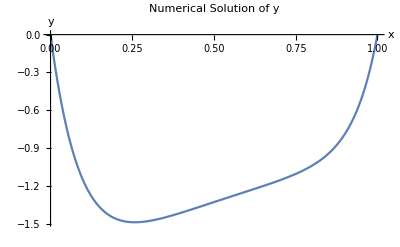

```mathematica
Show[graphy]
```

```mathematica
yhand[x_]:=2 ⅇ^(-x/0.01^(1/2))+ⅇ^(2^(1/2) ((x-1)/0.01^(1/2)))-2/(1+ x)
```

```mathematica
graphyh=Plot[yhand[x],{x,0,1},AxesLabel->{"t","y"},PlotLabel->"Analytic Solution of y"];
```

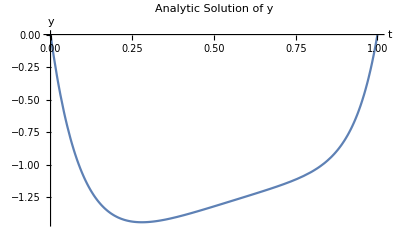

```mathematica
Show[graphyh]
```

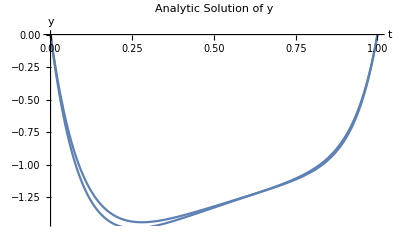

```mathematica
Show[graphyh,graphy]
```